```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lyazj/software/muemue/qe

```mathematica
$Post=If[MatrixQ[#],MatrixForm[#],#]&
```

If[MatrixQ[#1],#1,#1]&

```mathematica
Get["DesnityMatrix_160GeV.mx"]
```

```mathematica
rho2//MatrixForm
```

```mathematica
Transpose[rho2]==rho2
```

```mathematica
Alep = {Subscript[SuperPlus[B], 1], Subscript[SuperPlus[B], 2], Subscript[SuperPlus[B], 3]}
Blep = {Subscript[SuperMinus[B], 1], Subscript[SuperMinus[B], 2], Subscript[SuperMinus[B], 3]}
```

{(B^+)_1,(B^+)_2,(B^+)_3}

{(B^-)_1,(B^-)_2,(B^-)_3}

```mathematica
Cmat = {{C11, C12, C13},{C21, C22, C23},{C31, C32, C33}}
```

(C11 | C12 | C13
C21 | C22 | C23
C31 | C32 | C33)

```mathematica
Rho2Qubit = (IdentityMatrix[4]+
Sum[Alep[[i]]*KroneckerProduct[PauliMatrix[i],IdentityMatrix[2]],{i, 3}]+
Sum[Blep[[j]]*KroneckerProduct[IdentityMatrix[2],PauliMatrix[j]],{j, 3}]+
Sum[Cmat[[i, j]]*KroneckerProduct[PauliMatrix[i], PauliMatrix[j]],{i,3},{j, 3}]
)
```

((B^-)_3+(B^+)_3+C33+1 | (B^-)_1-ⅈ (B^-)_2+C31-ⅈ C32 | (B^+)_1-ⅈ (B^+)_2+C13-ⅈ C23 | C11-ⅈ C12-ⅈ C21-C22
(B^-)_1+ⅈ (B^-)_2+C31+ⅈ C32 | -(B^-)_3+(B^+)_3-C33+1 | C11+ⅈ C12-ⅈ C21+C22 | (B^+)_1-ⅈ (B^+)_2-C13+ⅈ C23
(B^+)_1+ⅈ (B^+)_2+C13+ⅈ C23 | C11-ⅈ C12+ⅈ C21+C22 | (B^-)_3-(B^+)_3-C33+1 | (B^-)_1-ⅈ (B^-)_2-C31+ⅈ C32
C11+ⅈ C12+ⅈ C21-C22 | (B^+)_1+ⅈ (B^+)_2-C13-ⅈ C23 | (B^-)_1+ⅈ (B^-)_2-C31-ⅈ C32 | -(B^-)_3-(B^+)_3+C33+1)

```mathematica
Bplus = Table[Tr[rho2.KroneckerProduct[PauliMatrix[i], IdentityMatrix[2]]],{i, 3}]//Simplify//Chop;
```

```mathematica
Bminus = Table[Tr[rho2.KroneckerProduct[IdentityMatrix[2], PauliMatrix[i]]],{i, 3}]//Simplify//Chop;
```

```mathematica
Cmatrix= Table[Tr[rho2.KroneckerProduct[PauliMatrix[i], PauliMatrix[j]]],{i, 3},{j, 3}]//Simplify//Chop;
```

```mathematica
pdmFunction[th1_, th2_, Emu_]:=rho2/.{E3->Emu, Subscript[θ, 1]->th1, Subscript[θ, 2]->th2}
```

```mathematica
(*****************************
muemue_example_1.0GeV_pT_4e-03GeV_E_5e-02GeV
muemue_example_10.0GeV_pT_3e-02GeV_E_1e+00GeV
muemue_example_10.0GeV_pT_3e-02GeV_E_1e-01GeV
muemue_example_160.0GeV_pT_1e-01GeV_E_1e+00GeV
muemue_example_160.0GeV_pT_1e-03GeV_E_1e-01GeV
**************************)
```

```mathematica
data= Import["muemue_example_160.0GeV_pT_1e-01GeV_E_1e+00GeV.txt", "Table"];
```

```mathematica
theta1= data[[All, 1]];
theta2= data[[All, 2]];
Emu= data[[All, 3]];
```

```mathematica
npts =10000;
```

```mathematica
iRho=Table[ pdmFunction[ theta1[[i]],theta2[[i]],Emu[[i]] ],{i, 1, npts}];
```

```mathematica
iRho[[1]]
```

(0.274835 | 0.250695 | 0.249319 | 0.272567
0.250695 | 0.228675 | 0.22742 | 0.248626
0.249319 | 0.22742 | 0.226172 | 0.247261
0.272567 | 0.248626 | 0.247261 | 0.270317)

```mathematica
TRrho2=Table[Tr[rho2]/.{E3->Emu[[i]], Subscript[θ, 1]->theta1[[i]], Subscript[θ, 2]->theta2[[i]]},{i, npts}]//Simplify//Chop;
```

```mathematica
TRrho2[[;;100]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
iRhoStar = Table[KroneckerProduct[PauliMatrix[2], PauliMatrix[2]].iRho[[k]].KroneckerProduct[PauliMatrix[2], PauliMatrix[2]],{k, 1, npts}];
```

```mathematica
Rmatrix=Table[iRho[[k]].iRhoStar[[k]],{k, 1, npts}];
```

```mathematica
eiValRmatrix =Table[√(Eigenvalues[Rmatrix[[k]]] //Chop[#, 10^-9]&)//Sort[#,Greater]&,{k, 1, npts}];
```

```mathematica
Crho=Table[Max[0, eiValRmatrix[[i]][[1]]- eiValRmatrix[[i]][[2]]-eiValRmatrix[[i]][[3]]-eiValRmatrix[[i]][[4]]],{i, 1, npts}];
```

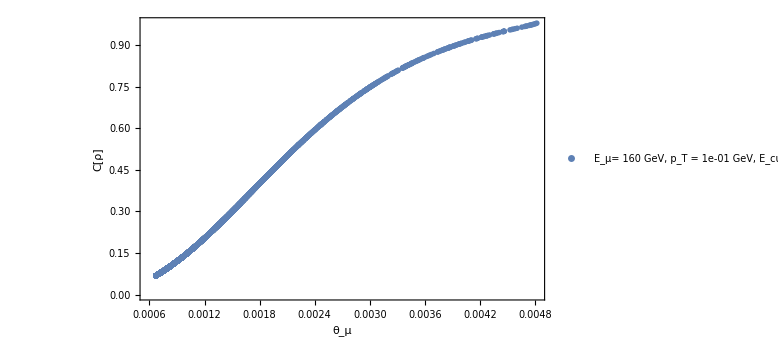

```mathematica
ListPlot[{
Transpose[{ theta1[[;;npts]],Crho}]
},Frame->True,FrameLabel->{"θ_μ","C[ρ]"},FrameStyle->Thick , PlotMarkers->{Automatic, 0.02},PlotLegends->Placed[{"E_μ= 160 GeV, p_T = 1e-01 GeV, E_cut = 1 GeV"},{0.4,0.8}],ImageSize->Large, PlotRange->{All,All}]
```

```mathematica
Mean[Crho]
```

0.00657731

```mathematica
(*Partial transpose of the density matrix*)
```

```mathematica
iRhoPartial = Table[ArrayFlatten[ Table[Partition[iRho[[k]], {2,2}][[i, j]]//Transpose,{i,2},{j,2}]],{k, 1, npts}];
```

```mathematica
ivaliPartial = Table[Eigenvalues[iRhoPartial[[k]]],{k, 1, npts}];
```

```mathematica
ivaliPartial[[1]]
```

{0.99928,-0.0268259,0.0268259,0.000720148}

```mathematica
iRhoPartialSmall=Table[{{iRhoPartial[[k]][[1,1]],iRhoPartial[[k]][[1,4]]},{iRhoPartial[[k]][[4,1]],iRhoPartial[[k]][[4,4]]}},{k, 1, npts}];
```

```mathematica
DETiRhoParSml= Table[Det[iRhoPartial[[k]]],{k, 1, npts}];
```

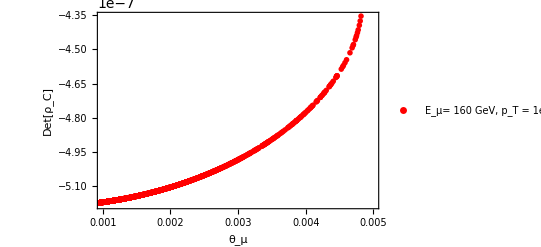

```mathematica
ListPlot[Transpose[{ theta1[[;;npts]],DETiRhoParSml}], Frame->True,PlotStyle->{Red,PointSize[0.01]},FrameLabel->{"θ_μ","Det[ρ_C]"},FrameStyle->Thick, PlotRange->{{0.001,0.005}, All},PlotLegends->{"E_μ= 160 GeV, p_T = 1e-03 GeV"}]
```

```mathematica
DETiRhoParSml[[4]]
```

0.00099431

```mathematica
(*Eigenvalue of the partial transpose*)
```

```mathematica
iEivalPartial = Table[Eigenvalues[iRhoPartial[[i]]],{i, npts}];
```

```mathematica
logNegativ=Table[Log2[2Sum[(Abs[iEivalPartial[[k]][[i]]] - iEivalPartial[[k]][[i]])/2,{i, 4}]+1],{k, npts}];
```

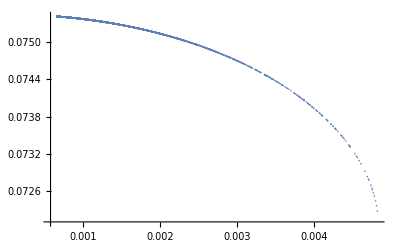

```mathematica
ListPlot[Transpose[{theta1[[;;npts]], logNegativ}], PlotRange->All]
```

```mathematica
cm33 = Table[Cmatrix[[3,3]]/.{Subscript[θ, 1]->theta1[[k]], Subscript[θ, 2]->theta2[[k]], E3->Emu[[k]]}, {k, 1, npts}];
cm11 = Table[Cmatrix[[1,1]]/.{Subscript[θ, 1]->theta1[[k]], Subscript[θ, 2]->theta2[[k]], E3->Emu[[k]]},{k, 1, npts}];
cm22 = Table[Cmatrix[[2,2]]/.{Subscript[θ, 1]->theta1[[k]], Subscript[θ, 2]->theta2[[k]], E3->Emu[[k]]},{k, 1, npts}];
```

```mathematica
delta = Table[-cm33[[k]]+Abs[cm11[[k]]+cm22[[k]]]-1,{k, 1, npts}];
```

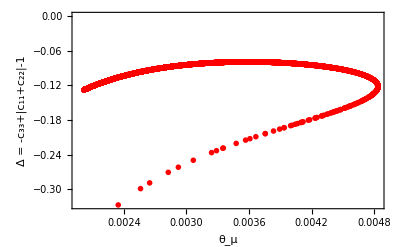

```mathematica
ListPlot[Transpose[{theta1[[;;npts]], delta}],Frame->True,PlotStyle->{Red, PointSize[0.01]},FrameLabel->{"θ_μ","Δ = -c_33+|c_11+c_22|-1"}, FrameStyle->Thick, PlotRange->All]
```

```mathematica
Ctrace = Table[Tr[Cmatrix/.{Subscript[θ, 1]->theta1[[k]], Subscript[θ, 2]->theta2[[k]], E3->Emu[[k]]}],{k, 1, npts}];
```

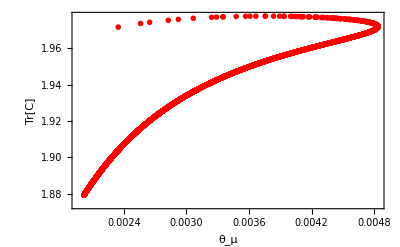

```mathematica
ListPlot[Transpose[{theta1[[;;npts]], Ctrace+1}],Frame->True,PlotStyle->{Red, PointSize[0.01]},FrameLabel->{"θ_μ","Tr[C]"}, FrameStyle->Thick, PlotRange->{Automatic,Automatic}]
```